## Oscillator disturbance rejection for uncertain frequency using Optimal derivative control (Problem 9.3)

```mathematica
Clear["Global`*"];
```

```mathematica
eqs={x''[t]+ω^2 x[t]==u[t],u[t]==-Kd x'[t], x[0]==0,x'[0]==1};
{xs,us}=DSolveValue[eqs,{x[t],u[t]},t,Assumptions->{Kd>0,ω>0,Kd^2-4 ω^2<0}]//FullSimplify ;  TraditionalForm[{xs,us}]
```

{(2 ⅇ^(-(Kd t)/2) sin(1/2 t √(4 ω^2-Kd^2)))/(√(4 ω^2-Kd^2)),Kd ⅇ^(-(Kd t)/2) ((Kd sin(1/2 t √(4 ω^2-Kd^2)))/(√(4 ω^2-Kd^2))-cos(1/2 t √(4 ω^2-Kd^2)))}

Both over- and underdamped responses give same functional form for cost function j, so the form given here applies to be both cases, with Cosh → Cos, etc. for the underdamped case.

Also:  time has been scaled so that ω_0=1.

```mathematica
J=Integrate[(xs^2+ us^2),{t,0,∞},Assumptions->{ω>0,Kd>0,Kd^2-4 ω^2>0}]//Simplify
```

(Kd^2+1/ω^2)/(2 Kd)

```mathematica
{Kd0=Kd/.Solve[D[J, Kd]==0/.ω->1,Kd][[2,1]],J0=J/.{ω->1,Kd->Kd0}}
```

{1,1}

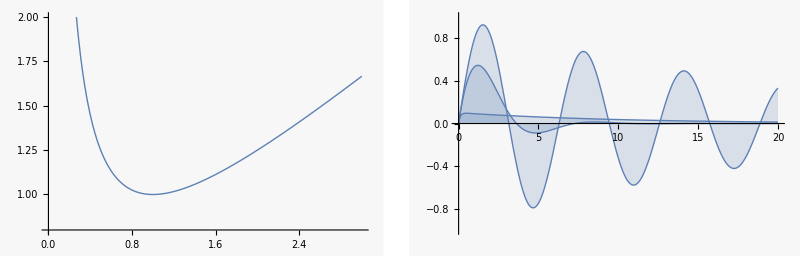

```mathematica
p1=Plot[J/.ω->1,{Kd,0,3},PlotRange->{0.8,2}];
p2=Plot[{xs//.{ω->1,Kd->{0.1Kd0,Kd0,10Kd0}}},{t,0,20},PlotRange->{-1,1},Filling->Axis];
GraphicsRow[{p1,p2},ImageSize->Full]
```

Introduce scaled quantities

```mathematica
{j=J/.Kd->k Kd0//Simplify,j/.{k->1,ω->1}}
```

{(k^2+1/ω^2)/(2 k),1}

```mathematica
α=-1/2(D[j, ω,ω,k]/D[j, k,k])/.{ω->1,k->1}
```

3/2

```mathematica
{D[j, ω,ω],D[j, ω,ω,ω,ω],D[j, k,k],D[j, ω,ω,k]}//Simplify
```

{3/(k ω^4),60/(k ω^6),1/(k^3 ω^2),-3/(k^2 ω^4)}

```mathematica
jstar=1+1/2 D[j, ω,ω] ϵ^2+1/(4!)D[j, ω,ω,ω,ω] 3 ϵ^4-1/2 D[j, k,k] ϵ^4/.{ω->1,k->1}
```

1+(3 ϵ^2)/2+7 ϵ^4

Series expansions

```mathematica
js=Series[j/.{ω->1+ϵ, k->1+α ϵ^2},{ϵ,0,4}]//Simplify//Normal
```

1-ϵ+(3 ϵ^2)/2-ϵ^3/2+(11 ϵ^4)/8

stats with lognormal distribution

```mathematica
μ=-1/2 Log[1+ϵ^2];σ=√Log[1+ϵ^2];
Expectation[{ω,(ω-1)^2,(ω-1)^4,1/ω^2},ω\[Distributed]LogNormalDistribution[μ,σ]]
```

{1,ϵ^2,3 ϵ^4+16 ϵ^6+15 ϵ^8+6 ϵ^10+ϵ^12,(1+ϵ^2)^3}

```mathematica
j2=1/2(k+((1+ϵ^2)^3)/k); (*  exact j as a function of k  *)
```

```mathematica
{kexact,kpert,knaive}={k/.Solve[D[j2, k]==0,k][[2]],Series[kexact,{ϵ,0,2}]//Normal,1}
```

{(1+ϵ^2)^(3/2),(1+ϵ^2)^(3/2),1}

```mathematica
{jexact,jpert,jnaive}=j2/.k->{kexact,kpert,knaive}
```

{(1+ϵ^2)^(3/2),(1+ϵ^2)^(3/2),1/2 (1+(1+ϵ^2)^3)}

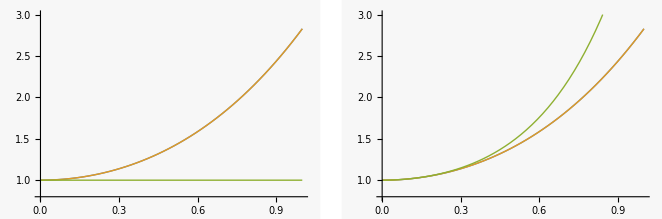

```mathematica
GraphicsRow[{
Plot[{kexact,kpert,knaive},{ϵ,0,1},PlotRange->{0.8,3}],
Plot[{jexact,jpert,jnaive},{ϵ,0,1},PlotRange->{0.8,3}]
},ImageSize->{662,219},AspectRatio->Full]
```

```mathematica
Series[j2/.k->kpert,{ϵ,0,8}]//Normal
```

1+(3 ϵ^2)/2+(3 ϵ^4)/8-ϵ^6/16+(3 ϵ^8)/128

```mathematica
Series[(1+ϵ^2)^(3/2),{ϵ,0,8}]//Normal
```

1+(3 ϵ^2)/2+(3 ϵ^4)/8-ϵ^6/16+(3 ϵ^8)/128